^2

# Mode III / anti-plane elasticity

## General settings for plots

```mathematica
(*Needs["MaTeX`"]*) (*<-- install MaTeX first, Latex in Wolfram *)
Needs["NDSolve`FEM`"]
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->14];
texStyle={FontFamily->"Arial",FontSize->14};
SetOptions[ContourPlot,Frame->True,FrameStyle-> Black,BaseStyle-> texStyle,AspectRatio->1,ImageSize->500];
```

```mathematica
SetOptions[Plot,Frame->True,FrameStyle-> Black,BaseStyle-> texStyle,AspectRatio->1,ImageSize->500];
SetOptions[ListPlot,Frame->True,FrameStyle-> Black,BaseStyle-> texStyle,AspectRatio->1,ImageSize->500];
```

## Relevant component of the stress tensor σ

```mathematica
σyz[x_,y_,l_,M_]:=(Abs[x] √(M^1-l^2+x^2-y^2)+Abs[y] √(M^1+l^2-x^2+y^2))/(√2 M)-1;
```

```mathematica
M[x_,y_,l_]:=√((-l+x)^2+y^2)√((l+x)^2+y^2);
```

“l” is half-crack length

## Coulomb stress change in parallel receiver faults

### Define Coulomb stress change on any parallel faults

```mathematica
CS[x_,y_,a_,f_]:=σyz[x,y,a,M[x,y,a]];
(* parallel faults are along x, "a" is half-crack length *)
```

Note that we are using classic solid mechanics convention
σyz is positive in the direction of slip of the receiver fault

Coulomb stress change on parallel faults due to crack of size 2a with unit stress drop

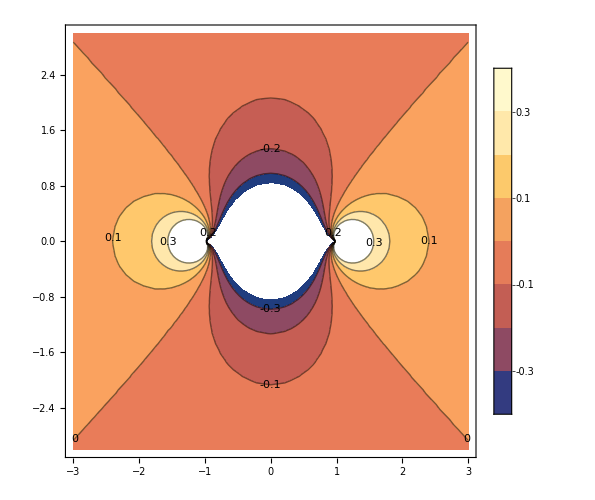

```mathematica
ContourPlot[CS[x,y,1.,0.6],{x,-3,3},{y,-3,3},PlotLegends->Automatic,ContourLabels->True,FrameLabel->{MaTeX["x/a"],MaTeX["y/a"]}]
```

### Coulomb stress change everywhere due to full rupture

#### Plot with dimensions in space (L=5km)

```mathematica
L=5.; (* crack/rupture length, km *)
AR=3.; (* aspect ratio of plot *)
f0=0.6; (* friction coefficient *)
```

Define the mesh/grid where CS is calculated (we use finite element package)

```mathematica
ΩDomain=Rectangle[{-L,-L*AR},{L,L*AR}]
```

Rectangle[{-5.,-15.},{5.,15.}]

```mathematica
(* function that makes the mesh finer in regions with high stress concentration *)
maxCellMeasure=500;
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[(x-L/2)^2+y^2<=(L/2)^2∨(x+L/2)^2+y^2<=(L/2)^2∨((-L/2<x<L/2)∧(-L/2/2<y<L/2/2)),area>0.0015,area>0.003* (3.+0.8 Norm[Mean[vertices]])]]];
```

```mathematica
mesh=ToElementMesh[ΩDomain,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,MeshRefinementFunction->f];
```

```mathematica
mesh["Wireframe"];
```

```mathematica
xyTab=mesh["Coordinates"];
xyTab//Dimensions
```

{29122,2}

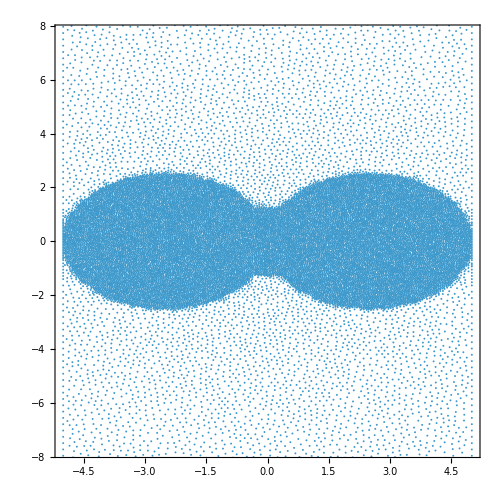

```mathematica
ListPlot@xyTab
```

Calculation of CS including a cap at too high (+limit) or too low (-limit) CS

```mathematica
limit=0.4;
```

```mathematica
CSdata=CS[#[[1]],#[[2]],L/2,f0]&/@xyTab;//AbsoluteTiming
```

{0.207028,Null}

```mathematica
negCS=Position[CSdata,_?(#<-limit&)]//Flatten;
posCS=Position[CSdata,_?(#>limit&)]//Flatten;
```

```mathematica
CSdataCapped=CSdata;
CSdataCapped[[negCS]]=-limit;
CSdataCapped[[posCS]]=limit;
```

```mathematica
dataCStoPlot={xyTab[[;;,1]],xyTab[[;;,2]],CSdataCapped}//Transpose;
```

```mathematica
(* our own color scheme *)
colorFun=Blend[{{0.,RGBColor[0,0,1]},{0.1,RGBColor[0,0.4,1]},{0.2,RGBColor[0,0.6,1]},{0.3,RGBColor[0,0.8,1]},{0.4,RGBColor[0,1,1]},{0.5,RGBColor[1,1,1]},{0.6,RGBColor[1,1,0]},{0.7,RGBColor[1.32,0.7,0.37]},{0.8,RGBColor[1.22,0.54,0.24]},{0.9,RGBColor[1.12,0.35,0.12]},{1.,RGBColor[1,0,0]}},#]&
```

Blend[{{0.,RGBColor[0, 0, 1]},{0.1,RGBColor[0, 0.4, 1]},{0.2,RGBColor[0, 0.6, 1]},{0.3,RGBColor[0, 0.8, 1]},{0.4,RGBColor[0, 1, 1]},{0.5,RGBColor[1, 1, 1]},{0.6,RGBColor[1, 1, 0]},{0.7,RGBColor[1.32, 0.7, 0.37]},{0.8,RGBColor[1.22, 0.54, 0.24]},{0.9,RGBColor[1.12, 0.35, 0.12]},{1.,RGBColor[1, 0, 0]}},#1]&

```mathematica
padding=80;
plotRange={{-L,L},{-AR*L,AR*L},{-limit,limit}};
plotRangeXY={{-L,L},{-AR*L,AR*L}};
```

```mathematica
densityPlot=ListDensityPlot[dataCStoPlot,ColorFunction->colorFun,
PlotRange->plotRange,
PlotRangePadding->Scaled[0.],
ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,
ImageSize->450,AspectRatio->AR];
```

```mathematica
sourceFault=Show[
Graphics[{FaceForm[White],Ellipsoid[{0,0},{L/2,(* fault thickness *)L/100}]}],
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
distanceFaults={1,3,5,10,20,30,60,120};(* receiver faults where we calculate CS afterwards, km *)
```

```mathematica
receiversTop=Show[
Graphics[{Black,Thickness[0.007],Line[{{-L/2,#},{L/2,#}}]}]&/@distanceFaults[[1;;4]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
receiversBottom=Show[
Graphics[{Black,Dashed,Thickness[0.007],Line[{{-L/2,-#},{L/2,-#}}]}]&/@distanceFaults[[1;;4]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
yTicks=Range[-AR*L,AR*L,2.5];
yTicksFrameTicksLeft={#,MaTeX[ToString[#]]}&/@yTicks;
yTicksFrameTicksRight={#,""}&/@yTicks;
```

```mathematica
xTicks=Range[-5,5,1];
xTicksFrameTicksBottom={#,MaTeX[ToString[#]]}&/@xTicks;
xTicksFrameTicksTop={#,""}&/@xTicks;
```

```mathematica
(*xGridLines=None;*)
xGridLines={Range[-5,5,1],ConstantArray[Dashed,Length@Range[-5,5,1]]}//Transpose;
```

```mathematica
axis=Graphics[Frame->True,PlotRange->plotRangeXY,AspectRatio->AR,FrameTicks->{{yTicksFrameTicksLeft,yTicksFrameTicksRight},{xTicksFrameTicksBottom,xTicksFrameTicksTop}},PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},ImageSize->450,LabelStyle->{16,Black,FontFamily->"Times"},FrameStyle->Black,GridLines->{xGridLines,None},FrameLabel->{MaTeX["x\\;(km)"],MaTeX["y\\;(km)"]}];
```

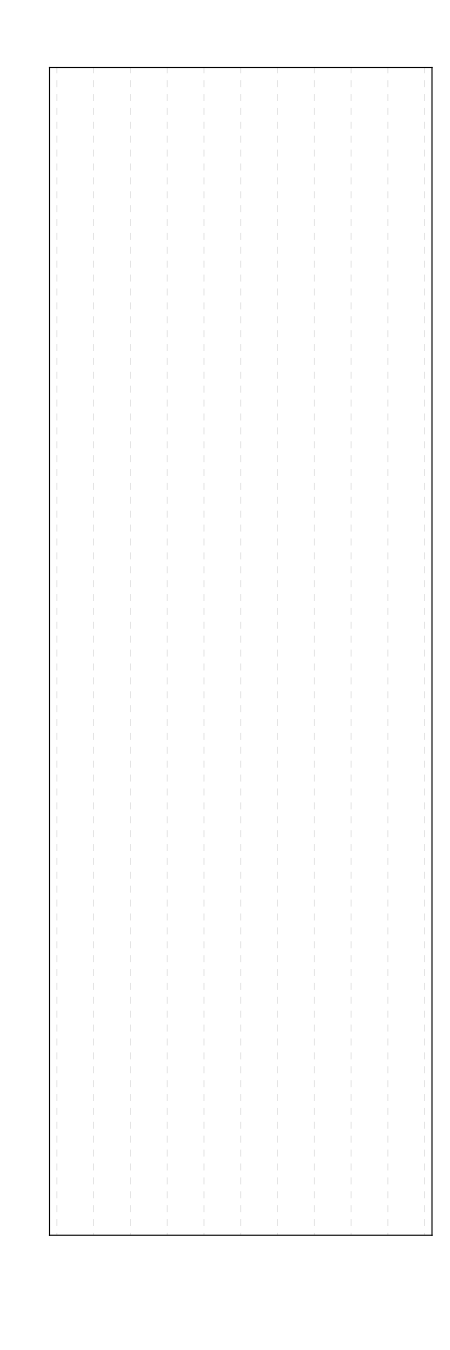
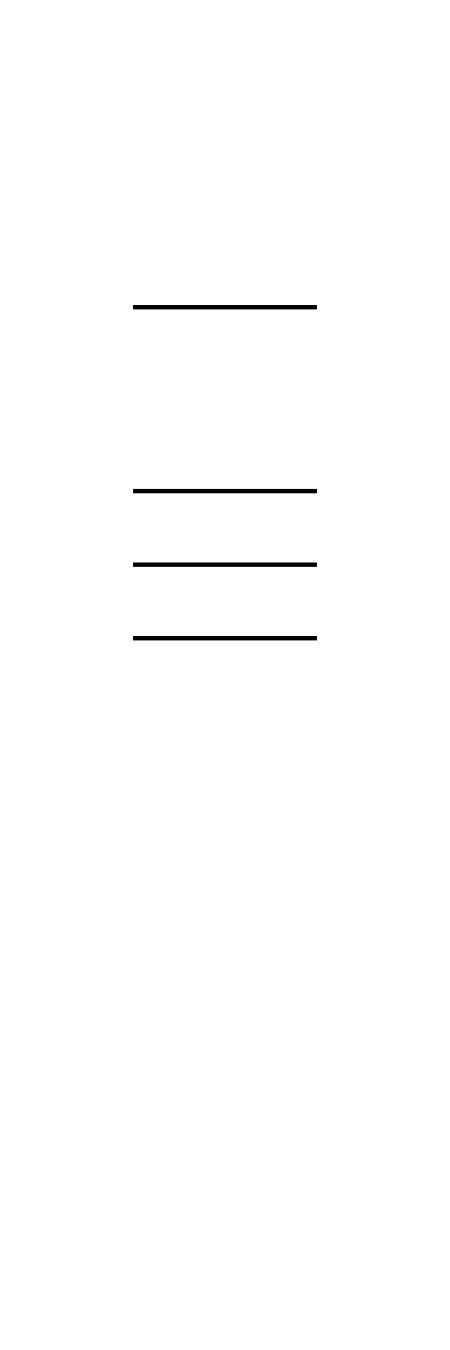
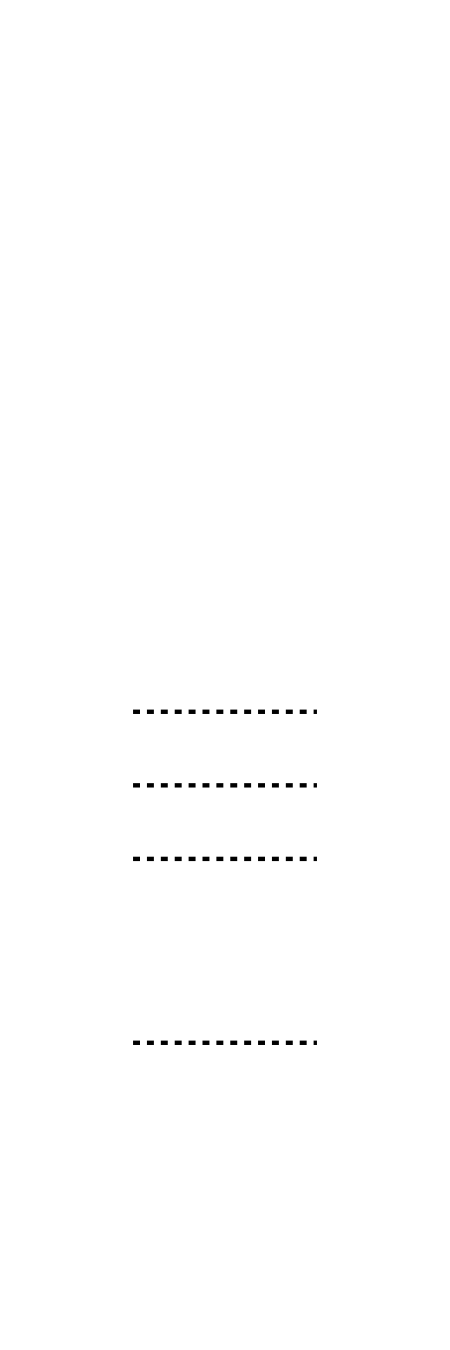
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Overlay[{densityPlot,sourceFault,axis,receiversTop,receiversBottom}]
```

Bar legend

```mathematica
BarLegend[{colorFun[(#+limit)/(2*limit)]&,{-limit,limit}},LegendMarkerSize->450,Method->{FrameStyle->Directive[Thickness[0.003],Black],"Ticks"->Automatic,TicksStyle->Directive[Thickness[0.003],Black]},LabelStyle->Directive[{FontFamily->"Times New Roman",FontSize->20,FontColor->Black}],LegendLayout->"Row"]
```

#### Dimensionless plot (crack/rupture in -0.5<x<0.5)

```mathematica
L=1.; (* crack/rupture length *)
AR=1.; (* aspect ratio of plot *)
f0=0.6; (* friction coefficient *)
```

Define the mesh/grid where CS is calculated (we use finite element package)

```mathematica
ΩDomain=Rectangle[{-L,-L*AR},{L,L*AR}]
(*h=L/1000;(* fault height *)*)
(*ΩFault=Rectangle[{-L/2-h/2,-h/2},{L/2+h/2,h/2}]*)
```

Rectangle[{-1.,-1.},{1.,1.}]

```mathematica
(* function that makes the mesh finer in regions with high stress concentration *)
maxCellMeasure=500;
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[(x-L/2)^2+y^2<=(L/2)^2∨(x+L/2)^2+y^2<=(L/2)^2∨((-L/2<x<L/2)∧(-L/2/2<y<L/2/2)),area>0.0015/16,area>0.003/16* (3.+0.8 Norm[Mean[vertices]])]]];
```

```mathematica
mesh=ToElementMesh[ΩDomain,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,MeshRefinementFunction->f];
```

```mathematica
mesh["Wireframe"];
```

```mathematica
xyTab=mesh["Coordinates"];
xyTab//Dimensions
```

{16759,2}

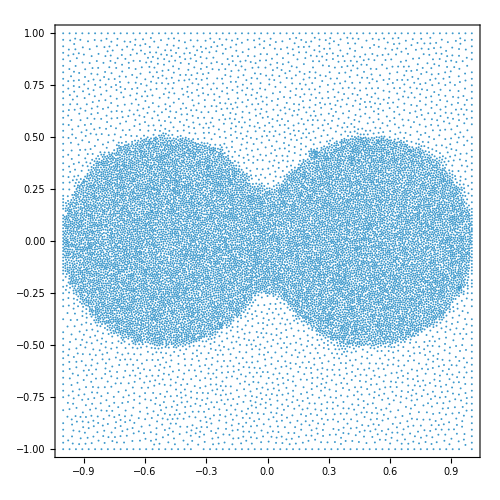

```mathematica
ListPlot@xyTab
```

Calculation of CS including a cap at too high (+limit) or too low (-limit) CS

```mathematica
limit=0.4;
```

```mathematica
CSdata=CS[#[[1]],#[[2]],L/2,f0]&/@xyTab;//AbsoluteTiming
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{0.132327,Null}

```mathematica
negCS=Position[CSdata,_?(#<-limit&)]//Flatten;
posCS=Position[CSdata,_?(#>limit&)]//Flatten;
```

```mathematica
CSdataCapped=CSdata;
CSdataCapped[[negCS]]=-limit;
CSdataCapped[[posCS]]=limit;
```

```mathematica
dataCStoPlot={xyTab[[;;,1]],xyTab[[;;,2]],CSdataCapped}//Transpose;
```

```mathematica
(* our own color scheme *)
colorFun=
Blend[{{0.0,RGBColor["#0F58A4"]},{0.5,RGBColor["#EBEADD"]},{1.0,RGBColor["Firebrick"]}},#]&
```

Blend[{{0.,RGBColor[#0F58A4]},{0.5,RGBColor[#EBEADD]},{1.,RGBColor[Firebrick]}},#1]&

```mathematica
padding=80;
plotRange={{-L,L},{-AR*L,AR*L},{-limit,limit}};
plotRangeXY={{-L,L},{-AR*L,AR*L}};
```

```mathematica
densityPlot=ListDensityPlot[dataCStoPlot,ColorFunction->colorFun,
PlotRange->plotRange,
PlotRangePadding->Scaled[0.],
ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ColorFunctionScaling->True,
ImageSize->450,AspectRatio->AR];
```

```mathematica
sourceFault=Show[
Graphics[{FaceForm[White],Ellipsoid[{0,0},{L/2,(* fault thickness *)L/100}]}],
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
Ldimensional=5.;(* km *)
distanceFaults={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional(* receiver faults where we calculate CS afterwards, note that all spatial distances are normalized by the crack length, L=1 in dimensionless plot *)
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
{0.04,0.1,0.2,0.6000000000000001,1.,2.,4.,6.,12.,24.}
```

{0.04,0.1,0.2,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
receiversTop=Show[
Graphics[{Black,Thickness[0.007],Line[{{-L/2,#},{L/2,#}}]}]&/@distanceFaults[[1;;6]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
receiversBottom=Show[
Graphics[{Black,Dashed,Thickness[0.007],Line[{{-L/2,-#},{L/2,-#}}]}]&/@distanceFaults[[1;;6]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
yTicks=Range[-AR*L,AR*L,0.5];
yTicksFrameTicksLeft={#,MaTeX[ToString[#]]}&/@yTicks;
yTicksFrameTicksRight={#,""}&/@yTicks;
```

```mathematica
xTicks=Range[-L,L,0.25];
xTicksFrameTicksBottom={#,MaTeX[ToString[#]]}&/@xTicks;
xTicksFrameTicksTop={#,""}&/@xTicks;
```

```mathematica
(*xGridLines=None;*)
xGridLines={Range[-L,L,0.25],ConstantArray[Dashed,Length@Range[-L,L,0.25]]}//Transpose;
```

Note: these grid lines are not at the “same” position as in the previous plot with dimensions in space

```mathematica
frameLabel={MaTeX["x/L_\\text{RW}"],MaTeX["y/L_\\text{RW}"]}
```

{-Graphics-,-Graphics-}

```mathematica
axis=Graphics[Frame->True,PlotRange->plotRangeXY,AspectRatio->AR,FrameTicks->{{yTicksFrameTicksLeft,yTicksFrameTicksRight},{xTicksFrameTicksBottom,xTicksFrameTicksTop}},PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},ImageSize->450,LabelStyle->{16,Black,FontFamily->"Arial"},FrameStyle->Black,GridLines->{xGridLines,None},FrameLabel->frameLabel];
```

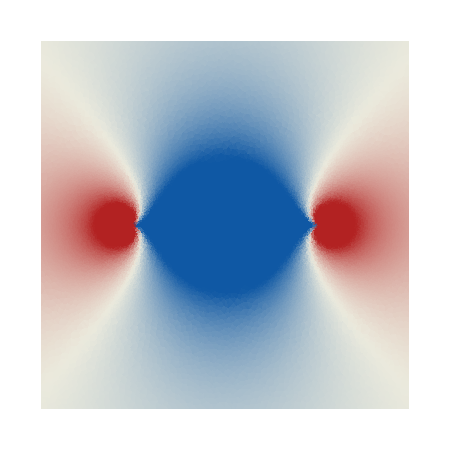
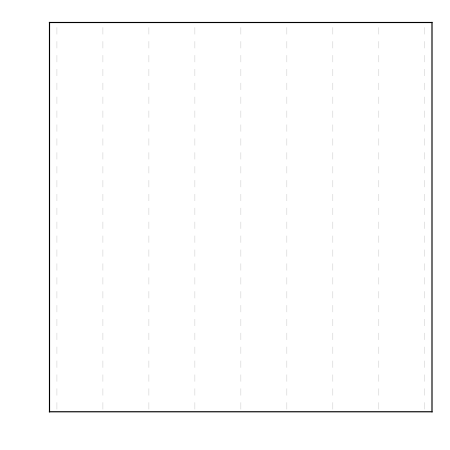
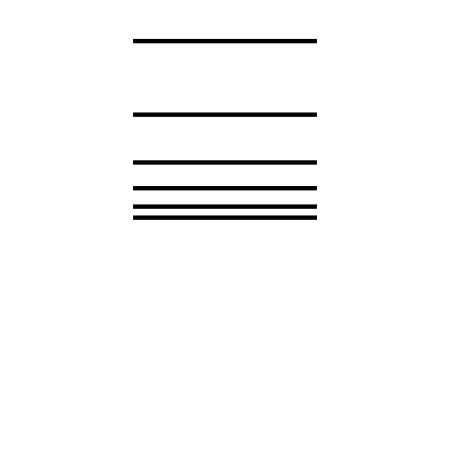
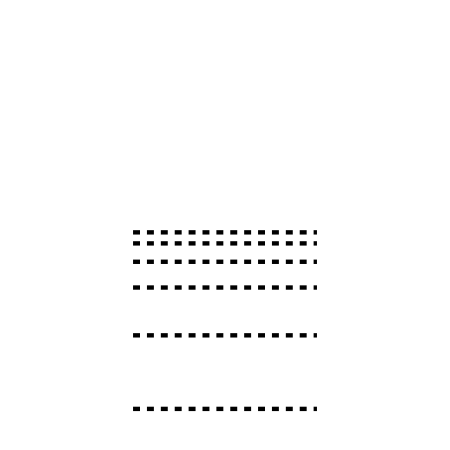
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Overlay[{densityPlot,sourceFault,axis,receiversTop,receiversBottom}]
```

```mathematica
(*build CSdataRaw as a list*)CSdataRaw=Quiet[CS[#[[1]],#[[2]],L/2,f0]&/@xyTab];

(*replace non-JSON values*)
CSdataForJSON=CSdataRaw/. {Indeterminate|ComplexInfinity|DirectedInfinity[_]->Null,Infinity->Null,-Infinity->Null};

(*make {x,y,cs} triples without Transpose*)
dataCStoPlotForJSON=MapThread[{#1[[1]],#1[[2]],#2}&,{xyTab,CSdataForJSON}];

Export["antiplane_full_CS.json",dataCStoPlotForJSON,"JSON"]
```

antiplane_full_CS.json

### Coulomb stress change along selected parallel faults due to full rupture

#### Plot with dimensions in space (L=5km)

```mathematica
L=5.; (* crack/rupture length, km *)
(*AR=3.; (* aspect ratio of plot *)*)
f0=0.6; (* friction coefficient *)
```

```mathematica
distanceFaults={1,3,5,10,20,30,60,120};(* receiver faults where we calculate CS, km *)
```

```mathematica
frameLabel={MaTeX["\\text{Distance along receiver fault, }x\\; (km)"],MaTeX["\\text{Normalized Coulomb stress change, }\\Delta S_\\text{receiver}/\\Delta\\tau_\\text{source}"]}
```

{-Graphics-,-Graphics-}

```mathematica
colors={Blue,Orange,Darker@Green,Red,Purple,Brown,Magenta,Gray}
```

{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5]}

```mathematica
legend=LineLegend[colors,Text[Style[ToString[#]<>" km",FontSize->12]]&/@distanceFaults]
```

Linear (normal) plot

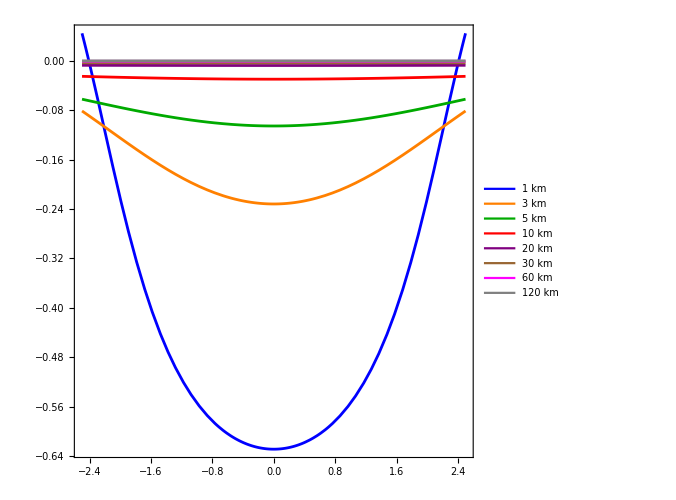

```mathematica
Show[
Plot[CS[x,distanceFaults[[1]],L/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[1]],PlotRange->{{-L/2,L/2},Automatic},PlotLegends->Placed[legend,{Left,Bottom}]],
Table[
Plot[CS[x,distanceFaults[[i]],L/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[i]],PlotRange->{{-L/2,L/2},Automatic}]
,{i,2,Length@distanceFaults}
]
]
```

Plot in log scale

```mathematica
minExp=-4;
maxExp=0;
stepExp=1;
tickY=Join[Table[{-10^i,MaTeX@Superscript[-10,i]},{i,minExp,maxExp,stepExp}]//Reverse,Table[{10^i,MaTeX@Superscript[10,i]},{i,minExp,maxExp,stepExp}]]
subtickY=Join[Table[{-10^i,""},{i,minExp,maxExp+1,stepExp}]//Reverse,Table[{10^i,""},{i,minExp,maxExp,stepExp}]]
```

{{-1,-Graphics-},{-1/10,-Graphics-},{-1/100,-Graphics-},{-1/1000,-Graphics-},{-1/10000,-Graphics-},{1/10000,-Graphics-},{1/1000,-Graphics-},{1/100,-Graphics-},{1/10,-Graphics-},{1,-Graphics-}}

{{-10,},{-1,},{-1/10,},{-1/100,},{-1/1000,},{-1/10000,},{1/10000,},{1/1000,},{1/100,},{1/10,},{1,}}

To allow for negative values in log scale

Source: https://jp.mathworks.com/matlabcentral/fileexchange/57902-symlog

```mathematica
logPosNeg[C_][x_]:=Sign[x]*Log10[1+Abs[x]/(10^C)];
```

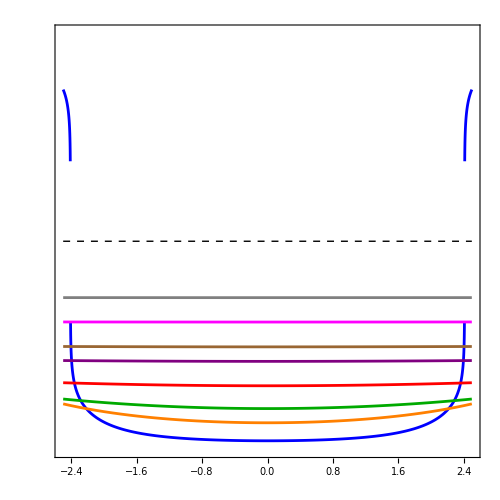

```mathematica
Show[
Table[
Plot[CS[x,distanceFaults[[i]],L/2.,f0],{x,-L/2,L/2},ScalingFunctions->{logPosNeg[minExp-1],logPosNeg[minExp-1]},Axes->{False,False},FrameTicks->{{Join[tickY,subtickY],subtickY},{Automatic,Automatic}},FrameLabel->frameLabel,PlotStyle->colors[[i]],PlotRange->{{-L/2,L/2},{-1,1}}]
,{i,Length@distanceFaults}
],
ListPlot[{{-L/2,0},{L/2,0}},Joined->True,PlotStyle->{Black,Dashed,Thickness[0.002]}](* y=0 line *)
]
```

We make a ListPlot to cross the y=0 line at small values of Coulomb stress change

```mathematica
nPts=10000.;
xTab=Range[-L/2,L/2,L/nPts];
xTab//Dimensions
```

{10001}

```mathematica
dataToPlot=Table[{xTab,CS[#,distanceFaults[[i]],L/2.,f0]&/@xTab}//Transpose,{i,Length@distanceFaults}];//AbsoluteTiming
```

{0.598457,Null}

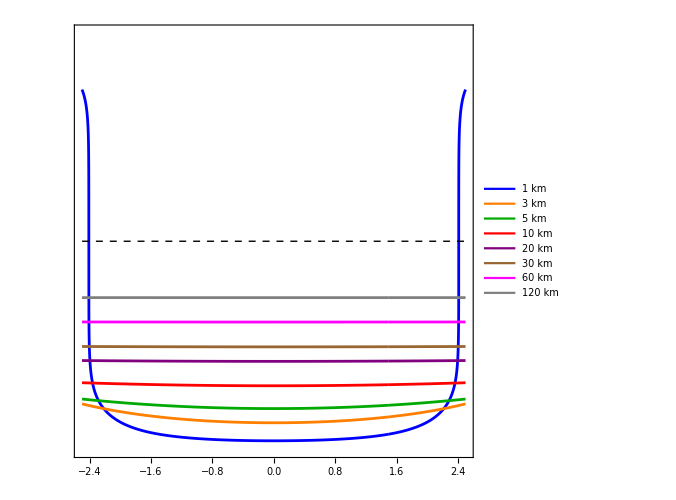

```mathematica
Show[
ListPlot[dataToPlot,ScalingFunctions->{logPosNeg[minExp-1],logPosNeg[minExp-1]},Axes->{False,False},Joined->True,FrameTicks->{{Join[tickY,subtickY],subtickY},{Automatic,Automatic}},FrameLabel->frameLabel,PlotStyle->colors,PlotRange->{{-L/2,L/2},{-1,1}},PlotLegends->Placed[legend,Right]]
,
ListPlot[{{-L/2,0},{L/2,0}},Joined->True,PlotStyle->{Black,Dashed,Thickness[0.002]}](* y=0 line *)
]
```

#### Dimensionless plot (crack/rupture in -0.5<x<0.5)

```mathematica
L=1.; (* crack/rupture length *)
f0=0.6; (* friction coefficient *)
```

```mathematica
Ldimensional=5.;(* km *)
distanceFaults={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional(* receiver faults where we calculate CS afterwards, note that all spatial distances are normalized by the half-crack length, therefore, L=1 in dimensionless plot *)
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
frameLabel={MaTeX["{\\Large \\text{Normalized distance along receiver fault, }x/L_\\text{RW}}","Preamble"->{"\\usepackage{helvet}","\\renewcommand{\\familydefault}{\\sfdefault}"}],MaTeX["{\\Large \\text{Normalized Coulomb stress change, }\\Delta S_\\text{receiver}/\\Delta\\tau_\\text{source}}","Preamble"->{"\\usepackage{helvet}","\\renewcommand{\\familydefault}{\\sfdefault}"}]};
```

```mathematica
colors={Blue,Orange,Darker@Green,Red,Purple,Brown,Magenta,Gray,Green,Yellow}
```

{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 1, 0]}

```mathematica
{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 1, 0],Cyan}
```

{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 1]}

```mathematica
{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],Green,Yellow}
```

{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 1, 0]}

```mathematica
DLParameter={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
legend=LineLegend[colors,Text[Style["D/L = "<>ToString[#],FontSize->12]]&/@DLParameter]
```

Linear (normal) plot

```mathematica
data=Table[First@Cases[Plot[CS[x,distanceFaults[[i]],L/2.,f0],{x,-L/2,L/2},PlotRange->All,PlotPoints->200]//Normal,Line[p_]:>p,∞],{i,1,Length@distanceFaults}];
Export["antiplane_full_rupture.json",data,"JSON"]
```

antiplane_full_rupture.json

Part::partw: Part 11 of {color,color,color,color,color,color,color,color,color,color} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

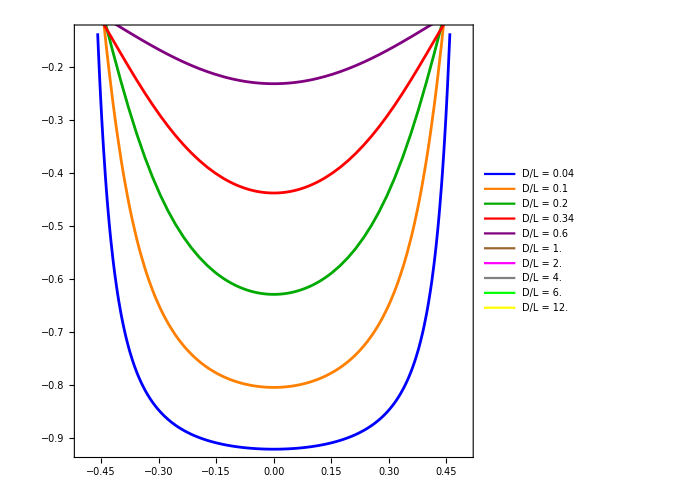

```mathematica
Show[
Plot[CS[x,distanceFaults[[1]],L/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[1]],PlotRange->{{-L/2,L/2},Automatic},PlotLegends->Placed[legend,{Left,Bottom}]],
Table[
Plot[CS[x,distanceFaults[[i]],L/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[i]],PlotRange->{{-L/2,L/2},Automatic}]
,{i,2,Length@distanceFaults}
]
]
```

Plot in log scale

```mathematica
minExp=-4;
maxExp=0;
stepExp=1;
tickY=Join[Table[{-10^i,MaTeX@Superscript[-10,i]},{i,minExp,maxExp,stepExp}]//Reverse,Table[{10^i,MaTeX@Superscript[10,i]},{i,minExp,maxExp,stepExp}]]
subtickY=Join[Table[{-10^i,""},{i,minExp,maxExp+1,stepExp}]//Reverse,Table[{10^i,""},{i,minExp,maxExp,stepExp}]]
```

{{-1,-Graphics-},{-1/10,-Graphics-},{-1/100,-Graphics-},{-1/1000,-Graphics-},{-1/10000,-Graphics-},{1/10000,-Graphics-},{1/1000,-Graphics-},{1/100,-Graphics-},{1/10,-Graphics-},{1,-Graphics-}}

{{-10,},{-1,},{-1/10,},{-1/100,},{-1/1000,},{-1/10000,},{1/10000,},{1/1000,},{1/100,},{1/10,},{1,}}

To allow for negative values in log scale

Source: https://jp.mathworks.com/matlabcentral/fileexchange/57902-symlog

```mathematica
logPosNeg[C_][x_]:=Sign[x]*Log10[1+Abs[x]/(10^C)];
```

```mathematica
nPts=10000.;
xTab=Range[-L/2,L/2,L/nPts];
xTab//Dimensions
```

{10001}

```mathematica
dataToPlot=Table[{xTab,CS[#,distanceFaults[[i]],L/2.,f0]&/@xTab}//Transpose,{i,Length@distanceFaults}];//AbsoluteTiming
```

{0.804675,Null}

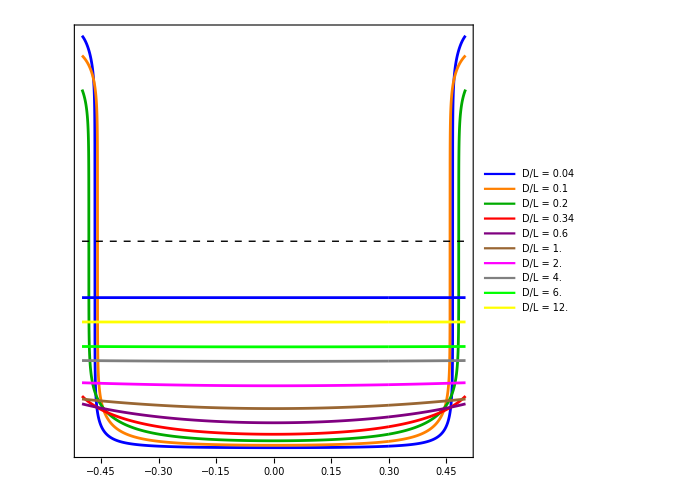

```mathematica
Show[
ListPlot[dataToPlot,ScalingFunctions->{logPosNeg[minExp-1],logPosNeg[minExp-1]},Axes->{False,False},Joined->True,FrameTicks->{{Join[tickY,subtickY],subtickY},{Automatic,Automatic}},FrameLabel->frameLabel,PlotStyle->colors,PlotRange->{{-L/2,L/2},{-1,1}},PlotLegends->Placed[legend,Right]]
,
ListPlot[{{-L/2,0},{L/2,0}},Joined->True,PlotStyle->{Black,Dashed,Thickness[0.002]}](* y=0 line *)
]
```

### Coulomb stress change everywhere due to partial rupture

#### Only dimensionless plot

```mathematica
L=1.;(* VW patch length *)
p=1/3.; (* length of partial rupture *)
AR=1.; (* aspect ratio of plot *)
f0=0.6; (* friction coefficient *)
```

Define the mesh/grid where CS is calculated (we use finite element package)

```mathematica
ΩDomain=Rectangle[{-(3L)/2+p/2,-L*AR},{L/2+p/2,L*AR}]
(*h=L/1000;(* fault height *)*)
(*ΩFault=Rectangle[{-L/2-h/2,-h/2},{L/2+h/2,h/2}]*)
```

Rectangle[{-1.33333,-1.},{0.666667,1.}]

```mathematica
(* function that makes the mesh finer in regions with high stress concentration *)
maxCellMeasure=500;
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[(x-p/2)^2+y^2<=(p/2)^2∨(x+p/2)^2+y^2<=(p/2)^2∨((-p/2<x<p/2)∧(-p/2/2<y<p/2/2)),area>0.0015/16,area>0.003/16* (3.+0.8 Norm[Mean[vertices]])]]];
```

```mathematica
mesh=ToElementMesh[ΩDomain,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,MeshRefinementFunction->f];
```

```mathematica
mesh["Wireframe"];
```

```mathematica
xyTab=mesh["Coordinates"];
xyTab//Dimensions
```

{6137,2}

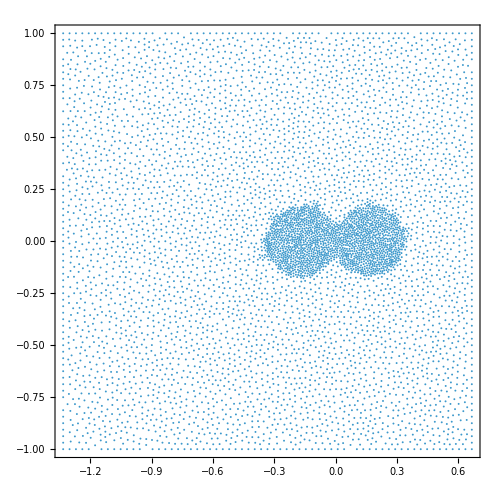

```mathematica
ListPlot@xyTab
```

Calculation of CS including a cap at too high (+limit) or too low (-limit) CS

```mathematica
limit=0.4;
```

```mathematica
CSdata=CS[#[[1]],#[[2]],p/2,f0]&/@xyTab;//AbsoluteTiming
```

{0.045112,Null}

```mathematica
negCS=Position[CSdata,_?(#<-limit&)]//Flatten;
posCS=Position[CSdata,_?(#>limit&)]//Flatten;
```

```mathematica
CSdataCapped=CSdata;
CSdataCapped[[negCS]]=-limit;
CSdataCapped[[posCS]]=limit;
```

```mathematica
dataCStoPlot={xyTab[[;;,1]]+(L-p)/2,xyTab[[;;,2]],CSdataCapped}//Transpose;
```

```mathematica
(* our own color scheme *)
colorFun=
Blend[{{0.0,RGBColor["#0F58A4"]},{0.5,RGBColor["#EBEADD"]},{1.0,RGBColor["Firebrick"]}},#]&
```

Blend[{{0.,RGBColor[#0F58A4]},{0.5,RGBColor[#EBEADD]},{1.,RGBColor[Firebrick]}},#1]&

```mathematica
padding=80;
```

```mathematica
plotRange={{-L,L},{-AR*L,AR*L},{-limit,limit}};
plotRangeXY={{-L,L},{-AR*L,AR*L}};
```

```mathematica
densityPlot=ListDensityPlot[dataCStoPlot,ColorFunction->colorFun,
PlotRange->plotRange,
PlotRangePadding->Scaled[0.],
ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ColorFunctionScaling->True,
ImageSize->450,AspectRatio->AR];
```

```mathematica
sourceFault=Show[
Graphics[{FaceForm[White],Ellipsoid[{(L-p)/2,0},{p/2,(* fault thickness *)L/100}]}],
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
Ldimensional=5.;(* km *)
distanceFaults={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional(* receiver faults where we calculate CS afterwards, note that all spatial distances are normalized by the crack length, L=1 in dimensionless plot *)
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
receiversTop=Show[
Graphics[{Black,Thickness[0.007],Line[{{-L/2,#},{L/2,#}}]}]&/@distanceFaults[[1;;4]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
receiversBottom=Show[
Graphics[{Black,Dashed,Thickness[0.007],Line[{{-L/2,-#},{L/2,-#}}]}]&/@distanceFaults[[1;;4]],(* plotting only first 4 receiver faults *)
PlotRange->plotRangeXY,PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},
Axes->False,Frame->False,ImageSize->450,AspectRatio->AR
];
```

```mathematica
yTicks=Range[-AR*L,AR*L,0.5];
yTicksFrameTicksLeft={#,MaTeX[ToString[#]]}&/@yTicks;
yTicksFrameTicksRight={#,""}&/@yTicks;
```

```mathematica
xTicks=Range[-L,L,0.25];
xTicksFrameTicksBottom={#,MaTeX[ToString[#]]}&/@xTicks;
xTicksFrameTicksTop={#,""}&/@xTicks;
```

```mathematica
(*xGridLines=None;*)
xGridLines={Range[-L,L,0.25],ConstantArray[Dashed,Length@Range[-L,L,0.25]]}//Transpose;
```

Note: these grid lines are not at the “same” position as in the previous plot with dimensions in space

```mathematica
frameLabel={MaTeX["x/L_\\text{RW}"],MaTeX["y/L_\\text{RW}"]}
```

{-Graphics-,-Graphics-}

```mathematica
axis=Graphics[Frame->True,PlotRange->plotRangeXY,AspectRatio->AR,FrameTicks->{{yTicksFrameTicksLeft,yTicksFrameTicksRight},{xTicksFrameTicksBottom,xTicksFrameTicksTop}},PlotRangePadding->Scaled[0.],ImagePadding->{{padding,padding},{padding,padding}},ImageSize->450,LabelStyle->{16,Black,FontFamily->"Times"},FrameStyle->Black,GridLines->{xGridLines,None},FrameLabel->frameLabel];
```

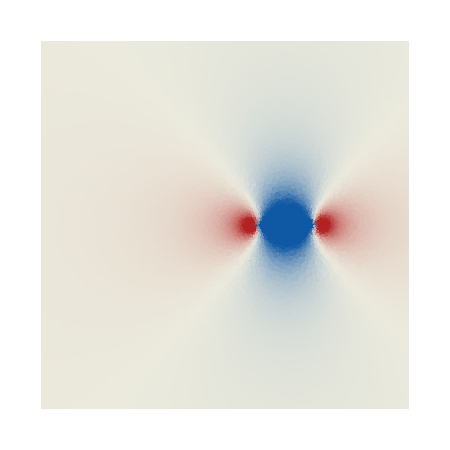
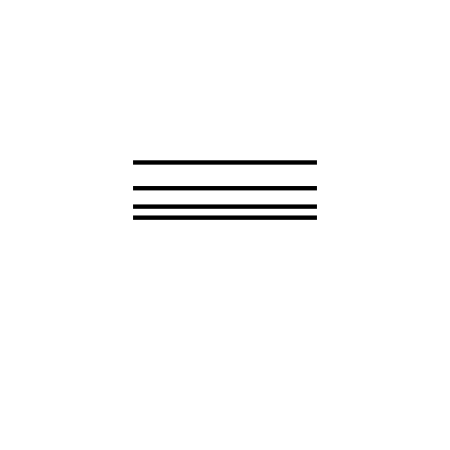
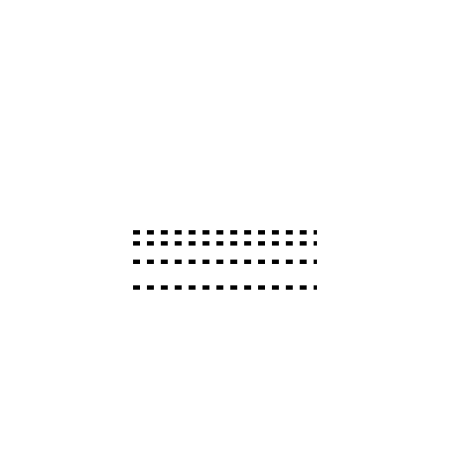
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Overlay[{densityPlot,sourceFault,axis,receiversTop,receiversBottom}]
```

```mathematica
(*second-plot shift (force numeric)*)shift2ForJSON=N[(L-p)/2];

(*build triples for the second density plot (NO Transpose issues)*)
dataCStoPlot2ForJSON=MapThread[{#1[[1]]+shift2ForJSON,#1[[2]],#2}&,{xyTab,CSdataCapped}];

(*JSON can't store Indeterminate/Infinity/Complex;convert to Null*)
dataCStoPlot2ForJSONClean=dataCStoPlot2ForJSON/. {Indeterminate|ComplexInfinity|DirectedInfinity[_]->Null,Infinity|-Infinity->Null,z_Complex:>Null};
dataCStoPlot2ForJSONNoNull=Select[dataCStoPlot2ForJSONClean,FreeQ[#,Null]&];

Export["antiplane_partial_CS.json",dataCStoPlot2ForJSONNoNull,"JSON"]
```

antiplane_partial_CS.json

### Coulomb stress change along selected parallel faults due to partial rupture

#### Only dimensionless plot

```mathematica
L=1.;(* VW patch length *)
p=1/3.; (* length of partial rupture *)
f0=0.6; (* friction coefficient *)
```

```mathematica
Ldimensional=5.;(* km *)
distanceFaults={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional(* receiver faults where we calculate CS afterwards, note that all spatial distances are normalized by the half-crack length, therefore, L=1 in dimensionless plot *)
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
{0.04000000000000001,0.1,0.2,0.6000000000000001,1.,12.,4.,6.,12.,24.}
```

{0.04,0.1,0.2,0.6,1.,12.,4.,6.,12.,24.}

```mathematica
frameLabel={MaTeX["{\\Large \\text{Normalized distance along receiver fault, }x/L_\\text{RW}}","Preamble"->{"\\usepackage{helvet}","\\renewcommand{\\familydefault}{\\sfdefault}"}],MaTeX["{\\Large \\text{Normalized Coulomb stress change, }\\Delta S_\\text{receiver}/\\Delta\\tau_\\text{source}}","Preamble"->{"\\usepackage{helvet}","\\renewcommand{\\familydefault}{\\sfdefault}"}]};
```

```mathematica
colors={Blue,Orange,Darker@Green,Red,Purple,Brown,Magenta,Gray,Green,Yellow,Cyan}
```

{RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5],RGBColor[0.6, 0.4, 0.2],RGBColor[1, 0, 1],GrayLevel[0.5],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 1]}

```mathematica
DLParameter={0.2,0.5,1,1.7,3,5,10,20,30,60,120}/Ldimensional
```

{0.04,0.1,0.2,0.34,0.6,1.,2.,4.,6.,12.,24.}

```mathematica
legend=LineLegend[colors,Text[Style["D/L = "<>ToString[#],FontSize->12]]&/@DLParameter]
```

Linear (normal) plot

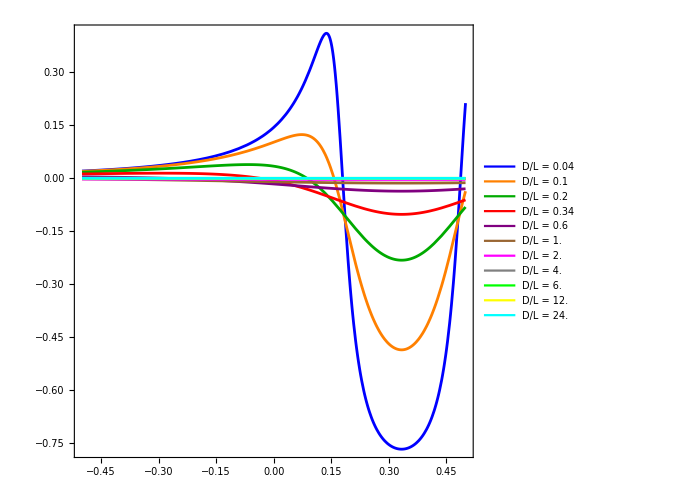

```mathematica
Show[
Plot[CS[x-(L-p)/2,distanceFaults[[1]],p/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[1]],PlotRange->{{-L/2,L/2},Automatic},PlotLegends->Placed[legend,{Left,Bottom}]],
Table[
Plot[CS[x-(L-p)/2,distanceFaults[[i]],p/2.,f0],{x,-L/2,L/2},FrameLabel->frameLabel,PlotStyle->colors[[i]],PlotRange->{{-L/2,L/2},Automatic}]
,{i,2,Length@distanceFaults}
]
]
```

Plot in log scale

```mathematica
minExp=-4;
maxExp=0;
stepExp=1;
tickY=Join[Table[{-10^i,MaTeX@Superscript[-10,i]},{i,minExp,maxExp,stepExp}]//Reverse,Table[{10^i,MaTeX@Superscript[10,i]},{i,minExp,maxExp,stepExp}]]
subtickY=Join[Table[{-10^i,""},{i,minExp,maxExp+1,stepExp}]//Reverse,Table[{10^i,""},{i,minExp,maxExp,stepExp}]]
```

{{-1,-Graphics-},{-1/10,-Graphics-},{-1/100,-Graphics-},{-1/1000,-Graphics-},{-1/10000,-Graphics-},{1/10000,-Graphics-},{1/1000,-Graphics-},{1/100,-Graphics-},{1/10,-Graphics-},{1,-Graphics-}}

{{-10,},{-1,},{-1/10,},{-1/100,},{-1/1000,},{-1/10000,},{1/10000,},{1/1000,},{1/100,},{1/10,},{1,}}

To allow for negative values in log scale

Source: https://jp.mathworks.com/matlabcentral/fileexchange/57902-symlog

```mathematica
logPosNeg[C_][x_]:=Sign[x]*Log10[1+Abs[x]/(10^C)];
```

```mathematica
nPts=10000.;
xTab=Range[-L/2,L/2,L/nPts];
xTab//Dimensions
```

{10001}

```mathematica
dataToPlot=Table[{xTab,CS[#-(L-p)/2,distanceFaults[[i]],p/2.,f0]&/@xTab}//Transpose,{i,Length@distanceFaults}];//AbsoluteTiming
```

{0.866789,Null}

```mathematica
Export["antiplane_partial_rupture.json",dataToPlot,"RawJSON"]
```

antiplane_partial_rupture.json

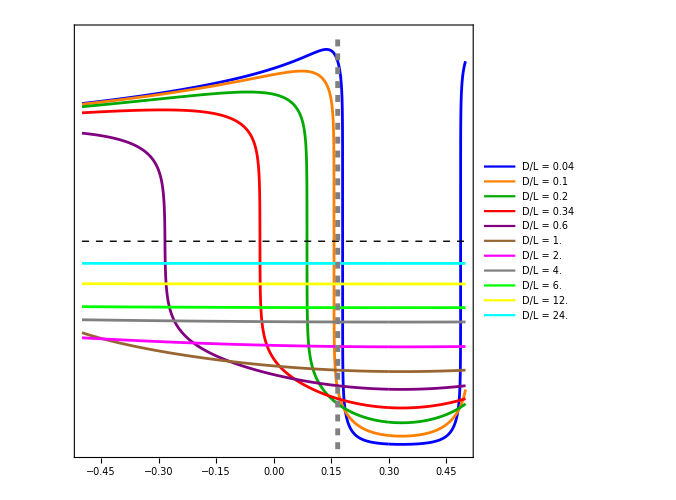

```mathematica
Show[
ListPlot[dataToPlot,ScalingFunctions->{logPosNeg[minExp-1],logPosNeg[minExp-1]},Axes->{False,False},Joined->True,FrameTicks->{{Join[tickY,subtickY],subtickY},{Automatic,Automatic}},FrameLabel->frameLabel,PlotStyle->colors,PlotRange->{{-L/2,L/2},{-1,1}},PlotLegends->Placed[legend,Right]]
,
ListPlot[{{-L/2,0},{L/2,0}},Joined->True,PlotStyle->{Black,Dashed,Thickness[0.002]}](* y=0 line *),
ListPlot[{{L/2-p,-1},{L/2-p,1}},ScalingFunctions->{logPosNeg[minExp-1],logPosNeg[minExp-1]},Joined->True,PlotStyle->{Gray,Dashed,Thickness[0.007]}](* y=0 line *)
]
```